```mathematica
ResourceFunction["DarkMode"][]
```

Output Locations

```mathematica
currDir = ToString[NotebookDirectory[]];
logDir = StringJoin[currDir, "output files/"];
```

Colour Templates
(uncomment displaySwatches[] to pick a colour!)

```mathematica
rybColourRules = {0->Red,1->Yellow,2->Blue};
rybDarkColourRules = "DarkRainbow";
fancyColourRules = "CandyColors";
blueColourRules = "DeepSeaColors";
pinkColourRules = "ValentineTones";
orangeColourRules = "SolarColors";
tigerColourRules = "SunsetColors";

displaySwatch[colourFunction_] := ArrayPlot[Mod[generateMaxHeightGrid[21],3], ColorFunction->colourFunction]

displaySwatches[] := Module[{gradients = ColorData["Gradients"], len = Length[ColorData["Gradients"]], swatches = {}, i = 0}, 
	Grid[ArrayReshape[Nest[Append[#, displaySwatch[gradients[[i++]]]] &, swatches, len + 1],{Ceiling[len / 6],6}]]]

(*displaySwatches[]*)
```

The following codeblock contains functions that will be evaluated either at the beginning or at the end of the simulation. They generate min/max height grids, and go between 3-coloured grids to height grids.

```mathematica
(* Generate the 'empty' grid with only the boundary cells filled in. Internal cells carry the value -1. *)
initialGridBorder[dim_] := initialGridBorder[dim] = 
	Normal[SparseArray[{{i_, j_} /; i == 1 || j == 1 -> i + j - 2, {i_, j_} /; i == dim || j == dim -> 2dim - i - j}, {dim, dim}, -1]]

(* Helper function for generateMaxHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMax[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] + 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] + 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] + 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] + 1; 
ReleaseHold[Hold[grid]])

(* Helper function for generateMinHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMin[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] - 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] - 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] - 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] - 1; 
ReleaseHold[Hold[grid]])

(* Generates the grid with maximum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMaxHeightGrid[dim_] := generateMaxHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMax[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Generates the grid with minimum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMinHeightGrid[dim_] := generateMinHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMin[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Takes a grid with a filled in height function as input and converts it to its corresponding 3-colouring form. *)
to3Colouring[grid_] := Mod[grid, 3]

(* Helper function for toHeightFunction *)
findListHeight[first_, list_, len_] := Module[{initialList = SparseArray[{}, {len}, -1], k = 0, prev = first}, (* remember that list is of length (len + 1) *)
 Nest[(k++; newList = #; prev = If[MemberQ[list[[{k, k + 1}]], 1], prev + list[[k + 1]] - list[[k]], If[list[[k]] == 2, prev + 1, prev - 1]]; newList[[k]] = prev; newList ) & , Normal[initialList], len]
]

(* Takes a 3-coloured grid as input and returns the corresponding grid labelled with its height values. *)
(* Edit: we now convert our grid to a 3-coloured grid before computing, so it gives the correct output on every grid! *)
(* Note: this starts with the initial border grid *)
toHeightFunction[grid_] := Module[{dim = Length[grid], heightGrid = initialGridBorder[Length[grid]], k = 1, cgrid = to3Colouring[grid]},
  Nest[(k++; nextHeightGrid = #; nextHeightGrid[[k, 2 ;; -2]] = findListHeight[heightGrid[[k, 1]], Normal[cgrid[[k, 1 ;; -2]]], dim - 2]; nextHeightGrid) &, heightGrid, dim - 2] 
] 

(* Calculates the sum of absolute differences between the heights of corresponding sites in the input grids *)
checkHeightDifference[grid1_, grid2_] := Total[Table[Abs[grid1[[i, j]] - grid2[[i, j]]], {i, 2, dim - 1}, {j, 2, dim - 1}], 2]

(* Format time *)
displayTime[time_] := DateString[time, {"Hour", ":", "Minute", ":", "Second"}]

(****** Display Functions ******)

(* Displays height grid matrix in array form *)
(* OPTIMISATION: check if you need to perform toHeightFunction! maybe check max value in grid? *)
displayHeightGrid[grid_] := ArrayPlot[grid, ColorFunction->"GrayTones"]

(* Displays height grid matrices in array form *)
displayHeightGrids[grid1_, grid2_] := Grid[{{displayHeightGrid[grid1], displayHeightGrid[grid2]}}]

(* Displays height grid matrix in array form *)
(* OPTIMISATION: check if you need to perform to3Coloring! maybe check max value in grid? *)
displayColouringGrid[grid_, colourFunction_] := ArrayPlot[to3Colouring[grid], ColorFunction->colourFunction]

(* Displays height grid matrices in array form *)
displayColouringGrids[grid1_, grid2_, colourFunction_] := Grid[{{displayColouringGrid[grid1, colourFunction], displayColouringGrid[grid2, colourFunction]}}]

displayHeightPlot[grid_] := ListPlot3D[grid]

displayHeightPlots[grid1_, grid2_] := Grid[{{displayHeightPlot[grid1], displayHeightPlot[grid2]}}]

displayGrids[grid1_, grid2_, colourFunction_] := Grid[{{displayHeightGrids[grid1, grid2]}, 
													  {displayColouringGrids[grid1, grid2, colourFunction]},
													  {displayHeightPlots[grid1, grid2]}}]
```

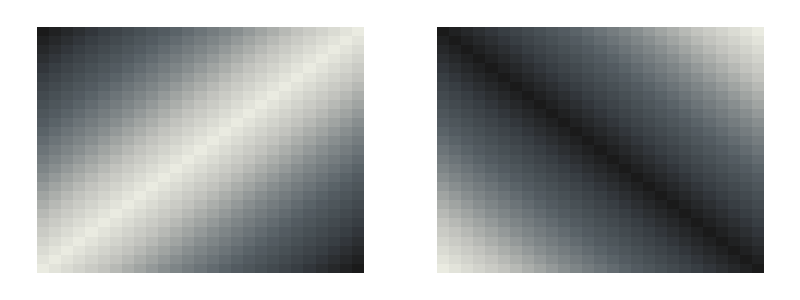
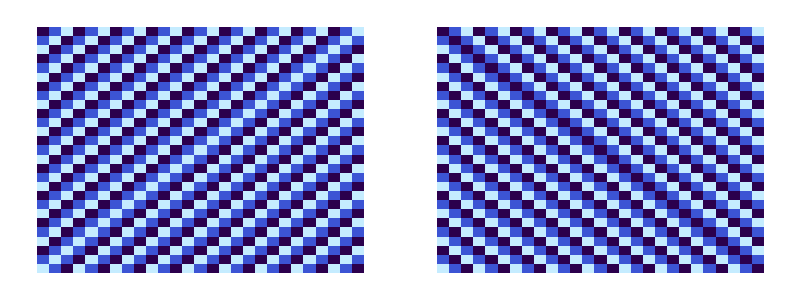
-Graphics-
-Graphics-
-Graphics3D- | -Graphics3D-

```mathematica
displayGrids[generateMaxHeightGrid[27],generateMinHeightGrid[27], blueColourRules]
```

Uncomment lines to view figures of grids and matrices.

```mathematica
(* Initial boundary grid with empty interior *)
Manipulate[{3(2k - 1), ArrayPlot[initialGridBorder[3(2k - 1)]]},{k,1,30,1}]

(*(* MaxHeightGrid matrix *)
MatrixForm[generateMaxHeightGrid[7], 7]

(* MaxHeightGrid array height function (black and white gradient) *)
Manipulate[ArrayPlot[generateMaxHeightGrid[3(2k - 1)]],{k,1,10,1}]

(* MaxHeightGrid array 3-colouring (candy colours) *)
Manipulate[ArrayPlot[Mod[generateMaxHeightGrid[3(2k - 1)], 3],  ColorFunction->fancyColourRules], {k,1,10,1}]

(* MinHeightGrid matrix *)
MatrixForm[generateMinHeightGrid[7], 7]

(* MinHeightGrid array height function (black and white gradient) *)
Manipulate[ArrayPlot[generateMinHeightGrid[3(2k - 1)]],{k,1,10,1}]

(* MinHeightGrid array 3-colouring (candy colours) *)
Manipulate[ArrayPlot[Mod[generateMinHeightGrid[3(2k - 1)], 3],  ColorFunction->fancyColourRules], {k,1,10,1}]
*)

(*Manipulate[displayHeightGrids[generateMinHeightGrid[3*(2*k - 1)], generateMaxHeightGrid[3*(2*k - 1)]], {k, 1, 20, 1}]
Manipulate[displayColouringGrids[generateMinHeightGrid[3*(2*k - 1)], generateMaxHeightGrid[3*(2*k - 1)], blueColourRules], {k, 1, 20, 1}]
Print["break"]*)
(*displayHeightGrids[generateMinHeightGrid[273], generateMaxHeightGrid[273]]
ArrayPlot[initialGridBorder[273]]*)
```

```mathematica
selectRandomSite[] := RandomChoice[Tuples[Range[2, dim - 1], 2]];
coinFlip[] := RandomChoice[{checkPopUp, checkPopDown}]
changeVal[grid_, pos_, newVal_] := ReplacePart[grid, pos -> newVal]

(* Check if you can pop up a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopUp[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 2 &]
(* Check if you can pop down a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopDown[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 1 &]

(* If heads, check if site can be popped up; otherwise, check if site can be popped down. *)
coinFunctionAssociation = Association[checkPopUp -> True, checkPopDown -> False];
coinSignAssociation = Association[checkPopUp -> Plus, checkPopDown -> Subtract];

(* coinTosses: list of random coin flips in the form of a list checkPopUp, checkPopDown functions *)
(* sites: list of random sites *)
(* generates numSteps new coin tosses and sites and adds them to the the beginning of existing lists *)
extendRandomLists[numSteps_] := (
	coinTosses = Join[Table[coinFlip[], numSteps], coinTosses];
	sites = Join[Table[selectRandomSite[], numSteps], sites];
)

(* Execute one step of the Markov chain on grid *)
(* OPTIMISATION: maybe put this in the function that performs multiple steps instead of calling it over and over? *)
oneStep[coin_, site_] := Module[{initialGrids = {maxGrid, minGrid}, outGrids = {maxGrid, minGrid}},
   Map[If[coin[initialGrids[[#]], site], 
   (outGrids[[#]] = changeVal[initialGrids[[#]], site, coinSignAssociation[coin][initialGrids[[#]][[Sequence @@ site]], 2]];)] &, {1, 2}];
   {maxGrid, minGrid} = outGrids;
]

(* Executes the algorithm for numSteps = len(coinTosses) steps *)
(* Additionally: logs files every numSteps/100 or 10 million steps, whichever is lower *)
(* Returns 1 if the grids converged, 0 if not*)
nStepsMarkovChain[] := Module[{numSteps = Length[coinTosses], logInterval = Min[10^7, Max[Round[Length[coinTosses] / 100], 20000]], outDir = StringJoin[logDir, "coupling_", ToString[dim], "/log_"],
	tempMinGrid, tempMaxGrid, tempHeightDifference, tempStepNumber, },
  Print["Running for ", numSteps, " steps..."];
  Print["Logging every ", logInterval, " steps"];
  Monitor[
    For[i = 0, i <= numSteps, i++, (
      If[Mod[i, logInterval] == 0 || checkHeightDifference[maxGrid, minGrid] == 0, 
       (Export[StringJoin[outDir, ToString[i], ".mx"], {maxGrid, minGrid}];
        {tempMinGrid, tempMaxGrid} = {minGrid, maxGrid};
        tempHeightDifference = checkHeightDifference[tempMinGrid, tempMaxGrid];
        tempStepNumber = i;
        (* WHAT IS THIS LINE DOING HERE? *)
        (*displayGrids[tempMaxGrid, tempMinGrid, blueColourRules];*)
        )
      ];
      (* OPTIMISATION: don't need to check height difference each time. If difference is 1000, only need to check again after 500 steps*)
      If[checkHeightDifference[maxGrid, minGrid] == 0, Return[1]];
      
      oneStep[coinTosses[[i]], sites[[i]]];)
    ], 
    Grid[{{StringJoin["Current step: ", ToString[tempStepNumber]]}, 
          {StringJoin["Height difference: ", ToString[tempHeightDifference]]}, 
          {displayGrids[tempMaxGrid, tempMinGrid, blueColourRules]}}
    ]
  ];
  Print["-- The height difference after ", numSteps, " was ", tempHeightDifference, "."];
  Return[0];
]


startChain[dimension_, t_] := Module[{coins, dirName = StringJoin[logDir, "coupling_", ToString[dimension], "/"], steps = t},
	dim = dimension;
	sites = {};
	coinTosses = {};
	converged = 0;	
	While[converged == 0, (
		(* Reset stuff *)
		{maxGrid, minGrid} = {generateMaxHeightGrid[dim], generateMinHeightGrid[dim]};
		DeleteDirectory[dirName, DeleteContents->True];
	    CreateDirectory[dirName];
	    
	    (* Generate new coin tosses and sites, and log them*)		
		extendRandomLists[steps];
		steps = Length[coinTosses];
		Export[StringJoin[dirName, "sites.csv"], sites, "CSV"];
		Export[StringJoin[dirName, "coin_tosses.csv"], coinTosses, "CSV"];
		
	    converged = nStepsMarkovChain[];
	)];
	
	Print["The chain took ", steps, " steps to converge. Here are the results:"];
	displayGrids[minGrid, maxGrid, blueColourRules];
]
```

Global Variables:
- maxGrid, minGrid
- coinTosses
- sites
- dim

```mathematica
(* testing oneStep *)
dim = 9;
maxGrid = generateMaxHeightGrid[dim];
minGrid = generateMinHeightGrid[dim];
maxGrid3 = to3Colouring[maxGrid];
minGrid3 = to3Colouring[minGrid];
Map[MatrixForm[#] &, {maxGrid, minGrid}]
Map[MatrixForm[#] &, {maxGrid3, minGrid3}]
oneStep[checkPopDown, {5,5}]
Map[MatrixForm[#] &, {maxGrid, minGrid}]
oneStep[checkPopDown, {4,6}]
Map[MatrixForm[#] &, {maxGrid, minGrid}]
Map[MatrixForm[#] &, {to3Colouring[generateMaxHeightGrid[dim]] - maxGrid, to3Colouring[generateMinHeightGrid[dim]] - minGrid}]
(* conclusion: oneStep works!*)
```

{(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 7
2 | 3 | 4 | 5 | 6 | 7 | 8 | 7 | 6
3 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5
4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4
5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3
6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2
7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0),(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6
3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5
4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4
5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3
6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2
7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0)}

{(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 1 | 2 | 0 | 1 | 2 | 1
2 | 0 | 1 | 2 | 0 | 1 | 2 | 1 | 0
0 | 1 | 2 | 0 | 1 | 2 | 1 | 0 | 2
1 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1
2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 0
0 | 1 | 2 | 1 | 0 | 2 | 1 | 0 | 2
1 | 2 | 1 | 0 | 2 | 1 | 0 | 2 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0),(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 1 | 2 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 1 | 2 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 2 | 1 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 2 | 1 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)}

{(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 7
2 | 3 | 4 | 5 | 6 | 7 | 8 | 7 | 6
3 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5
4 | 5 | 6 | 7 | 6 | 7 | 6 | 5 | 4
5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3
6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2
7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0),(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6
3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5
4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4
5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3
6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2
7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0)}

{(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 7
2 | 3 | 4 | 5 | 6 | 7 | 8 | 7 | 6
3 | 4 | 5 | 6 | 7 | 6 | 7 | 6 | 5
4 | 5 | 6 | 7 | 6 | 7 | 6 | 5 | 4
5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3
6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2
7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0),(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6
3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5
4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4
5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3
6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2
7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0)}

{(0 | 0 | 0 | -3 | -3 | -3 | -6 | -6 | -6
0 | 0 | -3 | -3 | -3 | -6 | -6 | -6 | -6
0 | -3 | -3 | -3 | -6 | -6 | -6 | -6 | -6
-3 | -3 | -3 | -6 | -6 | -4 | -6 | -6 | -3
-3 | -3 | -6 | -6 | -4 | -6 | -6 | -3 | -3
-3 | -6 | -6 | -6 | -6 | -6 | -3 | -3 | -3
-6 | -6 | -6 | -6 | -6 | -3 | -3 | -3 | 0
-6 | -6 | -6 | -6 | -3 | -3 | -3 | 0 | 0
-6 | -6 | -6 | -3 | -3 | -3 | 0 | 0 | 0),(0 | 0 | 0 | -3 | -3 | -3 | -6 | -6 | -6
0 | 0 | 0 | 0 | -3 | -3 | -3 | -6 | -6
0 | 0 | 0 | 0 | 0 | -3 | -3 | -3 | -6
-3 | 0 | 0 | 0 | 0 | 0 | -3 | -3 | -3
-3 | -3 | 0 | 0 | 0 | 0 | 0 | -3 | -3
-3 | -3 | -3 | 0 | 0 | 0 | 0 | 0 | -3
-6 | -3 | -3 | -3 | 0 | 0 | 0 | 0 | 0
-6 | -6 | -3 | -3 | -3 | 0 | 0 | 0 | 0
-6 | -6 | -6 | -3 | -3 | -3 | 0 | 0 | 0)}

```mathematica
(* testing extendRandomLists *)
arr1 = {};
arr2 = {};
sites = {};
coinTosses = {};
extendRandomLists[10];
Print["first:", sites, coinTosses]
extendRandomLists[10];
Print["second:", sites, coinTosses]
(* conclusion: extendedRandomLists works! *)
```

first:{{2,3},{2,2},{4,4},{2,3},{3,3},{2,2},{4,3},{4,2},{4,4},{3,3}}{checkPopUp,checkPopUp,checkPopUp,checkPopDown,checkPopUp,checkPopUp,checkPopDown,checkPopDown,checkPopDown,checkPopDown}

second:{{4,4},{3,3},{3,3},{2,3},{2,3},{3,3},{2,3},{2,2},{3,4},{2,3},{2,3},{2,2},{4,4},{2,3},{3,3},{2,2},{4,3},{4,2},{4,4},{3,3}}{checkPopDown,checkPopDown,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopUp,checkPopDown,checkPopUp,checkPopUp,checkPopDown,checkPopDown,checkPopDown,checkPopDown}

```mathematica
dim = 11;
maxGrid = generateMaxHeightGrid[dim];
minGrid = generateMinHeightGrid[dim];
coinTosses = {};
sites = {};
extendRandomLists[100000];
```

```mathematica
nStepsMarkovChain[]
```

Running a Markov Chain for 100000 steps...

1000/home/nupurj/Documents/Dimer Models/code/output files/coupling_11/log_

0

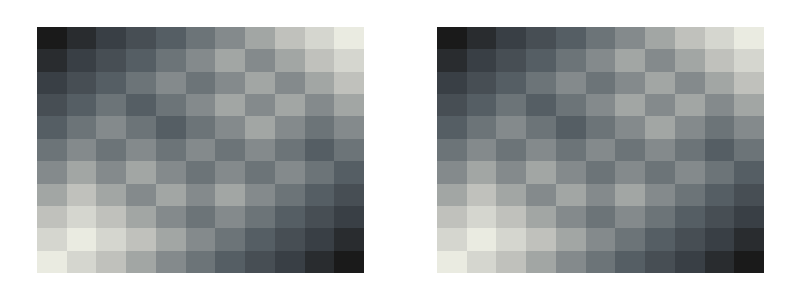
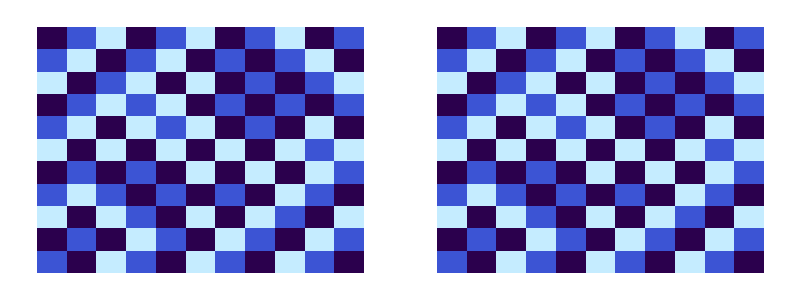

```mathematica
displayGrids[maxGrid, minGrid, blueColourRules]
```

```mathematica
displayGrids[Sequence @@ Import[StringJoin[logDir, "coupling_11/log_73966.mx"]], blueColourRules]
```

-Graphics-
-Graphics-
-Graphics3D- | -Graphics3D-

Remember: 
- ClearAll before starting over
- log coins and sites lists each time!!

- starts with t steps!

```mathematica
startChain[21, 500000]
```

Running for 500000 steps...

Logging every 20000 steps

```mathematica
displayGrids[Sequence @@ Import[StringJoin[logDir, "coupling_21/log_1584000.mx"]], blueColourRules]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0
0 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 0
0 | 2 | 4 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 16 | 16 | 16 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 18 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 18 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 16 | 16 | 16 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 4 | 2 | 0
0 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 0
0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

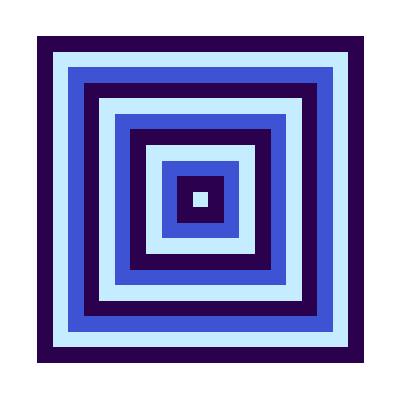

-Graphics-

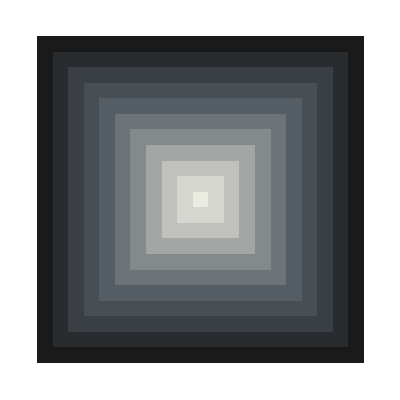

```mathematica
mintemp = generateMinHeightGrid[21];
maxtemp = generateMaxHeightGrid[21];
diff = maxtemp - mintemp;
TableForm[diff]

displayColouringGrid[diff, blueColourRules]
displayColouringGrid[to3Colouring[diff], blueColourRules]
displayHeightGrid[diff]
```

```mathematica
TableForm[diff]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0
0 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 0
0 | 2 | 4 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 16 | 16 | 16 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 18 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 18 | 18 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 16 | 16 | 16 | 16 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 6 | 4 | 2 | 0
0 | 2 | 4 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 4 | 2 | 0
0 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 0
0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
{tempmin, tempmax}  = Import[StringJoin[logDir, "coupling_21/log_340000.mx"]]
```

{{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,11,12,13,14,15,16,17,18,19},{2,3,4,5,6,7,8,9,10,11,12,11,12,11,12,13,14,15,16,17,18},{3,4,5,6,7,8,9,10,9,10,11,10,11,12,13,12,13,14,15,16,17},{4,5,6,7,8,9,10,9,8,9,10,11,12,13,12,13,14,13,14,15,16},{5,6,7,8,9,8,9,8,9,10,9,10,11,12,11,12,13,14,13,14,15},{6,7,8,9,8,9,8,7,8,9,8,9,10,11,12,11,12,13,12,13,14},{7,8,9,8,9,8,9,8,9,8,9,10,11,12,11,12,11,12,13,12,13},{8,9,8,9,8,7,8,9,10,9,10,9,10,11,12,11,10,11,12,11,12},{9,8,9,8,9,8,9,8,9,10,9,8,9,10,11,10,11,10,11,10,11},{10,9,10,9,10,9,10,9,10,11,10,9,10,9,10,9,10,9,10,9,10},{11,10,11,10,11,10,9,10,9,10,9,10,9,10,9,10,11,10,9,10,9},{12,11,12,11,10,9,8,9,8,9,8,9,10,9,8,9,10,9,8,9,8},{13,12,13,12,11,10,9,8,9,8,9,10,9,8,9,10,9,8,9,8,7},{14,13,12,13,12,11,10,9,10,9,10,9,8,7,8,9,10,9,8,7,6},{15,14,13,12,13,12,11,10,11,10,9,8,7,8,9,10,9,8,7,6,5},{16,15,14,13,12,13,12,11,10,9,10,9,8,7,8,9,8,7,6,5,4},{17,16,15,14,13,14,13,12,11,10,11,10,9,8,7,8,7,6,5,4,3},{18,17,16,15,14,15,14,13,12,11,10,9,8,9,8,7,6,5,4,3,2},{19,18,17,16,15,14,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}},{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,11,12,13,14,15,16,17,18,19},{2,3,4,5,6,7,8,9,10,11,12,11,12,11,12,13,14,15,16,17,18},{3,4,5,6,7,8,9,10,9,10,11,10,11,12,13,12,13,14,15,16,17},{4,5,6,7,8,9,10,9,8,9,10,11,12,13,12,13,14,13,14,15,16},{5,6,7,8,9,8,9,8,9,10,9,10,11,12,11,12,13,14,13,14,15},{6,7,8,9,8,9,8,7,8,9,8,9,10,11,12,11,12,13,12,13,14},{7,8,9,8,9,8,9,8,9,8,9,10,11,12,11,12,11,12,13,12,13},{8,9,8,9,8,7,8,9,10,9,10,9,10,11,12,11,10,11,12,11,12},{9,8,7,8,7,8,9,8,9,10,9,8,9,10,11,10,11,10,11,10,11},{10,9,8,9,8,9,10,9,10,11,10,9,10,9,10,9,10,9,10,9,10},{11,10,9,10,9,10,9,8,9,10,9,10,9,10,9,10,11,10,9,10,9},{12,11,10,11,10,9,8,9,8,9,8,9,10,9,8,9,10,9,8,9,8},{13,12,11,12,11,10,9,8,9,8,9,10,9,8,9,10,9,8,9,8,7},{14,13,12,11,12,11,10,9,10,9,10,9,8,7,8,9,10,9,8,7,6},{15,14,13,12,13,12,11,10,11,10,9,8,7,8,9,10,9,8,7,6,5},{16,15,14,13,12,13,12,11,10,9,10,9,8,7,8,9,8,7,6,5,4},{17,16,15,14,13,14,13,12,11,10,11,10,9,8,7,8,7,6,5,4,3},{18,17,16,15,14,15,14,13,12,11,10,9,8,9,8,7,6,5,4,3,2},{19,18,17,16,15,14,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}}}

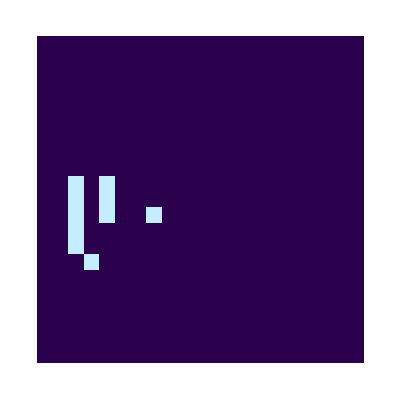

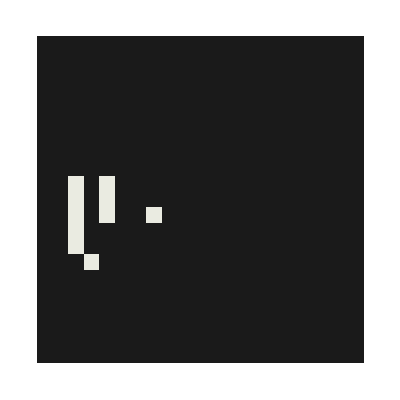

```mathematica
tempdiff = tempmin - tempmax;
displayColouringGrid[to3Colouring[tempdiff], blueColourRules]
displayHeightGrid[tempdiff]
```

```mathematica
TableForm[tempdiff]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
TableForm[tempmin]
TableForm[tempmax]
```

0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 15 | 16 | 17
4 | 5 | 6 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 16
5 | 6 | 7 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 14 | 13 | 14 | 15
6 | 7 | 8 | 9 | 8 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 12 | 13 | 14
7 | 8 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 11 | 12 | 13 | 12 | 13
8 | 9 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 11 | 12 | 11 | 12
9 | 8 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 11 | 10 | 11 | 10 | 11
10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 11 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10
11 | 10 | 11 | 10 | 11 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 11 | 10 | 9 | 10 | 9
12 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 8
13 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 8 | 7
14 | 13 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6
15 | 14 | 13 | 12 | 13 | 12 | 11 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5
16 | 15 | 14 | 13 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4
17 | 16 | 15 | 14 | 13 | 14 | 13 | 12 | 11 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 5 | 4 | 3
18 | 17 | 16 | 15 | 14 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2
19 | 18 | 17 | 16 | 15 | 14 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
20 | 19 | 18 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0

0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 15 | 16 | 17
4 | 5 | 6 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 16
5 | 6 | 7 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 14 | 13 | 14 | 15
6 | 7 | 8 | 9 | 8 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 12 | 13 | 14
7 | 8 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 11 | 12 | 11 | 12 | 11 | 12 | 13 | 12 | 13
8 | 9 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 11 | 12 | 11 | 12
9 | 8 | 7 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 11 | 10 | 11 | 10 | 11
10 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10
11 | 10 | 9 | 10 | 9 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 9 | 10 | 9 | 10 | 11 | 10 | 9 | 10 | 9
12 | 11 | 10 | 11 | 10 | 9 | 8 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 8
13 | 12 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 9 | 8 | 7
14 | 13 | 12 | 11 | 12 | 11 | 10 | 9 | 10 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6
15 | 14 | 13 | 12 | 13 | 12 | 11 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5
16 | 15 | 14 | 13 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4
17 | 16 | 15 | 14 | 13 | 14 | 13 | 12 | 11 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 5 | 4 | 3
18 | 17 | 16 | 15 | 14 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2
19 | 18 | 17 | 16 | 15 | 14 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
20 | 19 | 18 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0

```mathematica
□_□
```

```mathematica
checkHeightDifference[tempmax, tempmin]
```

132